Parameters

g_Pg = 0.0013

g_Ps = 0.0118

g_k = 0.0224

κ = 0.420204

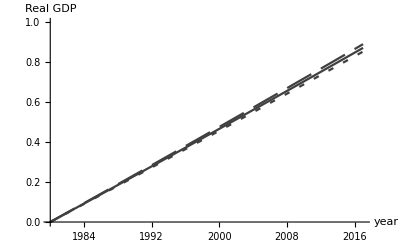

Diff Laspeyres minus Passhe at 2017:0.0619594

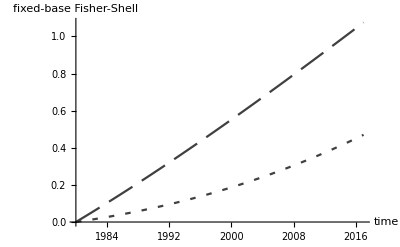

```mathematica
θ=1/3;ρ=0.04;δ=0.08; (*  from HRV *)
η=0.21370396;χ=0.22;γ=0.83;  (*  Nacho's estimation *)
(* η=0.44;χ=0.55;γ=0.69;*)

nn=0.0098; γg=0.0109;γs=0.0004;γx=0.0122;γh=0.0041;  (*  from HRV dataset *)

Ag0=1;As0=1;Ax0=1;  (* normalization *)

gpg=γx-γg;  Print["g_Pg = ",gpg] (*  growth rate Pg *)
gps=γx-γs;   Print["g_Ps = ",gps](*  growth rate Ps *)
gk=γx/(1-θ)+γh; Print["g_k = ",gk](*  growth rate k, e and y *)

κ=(ρ+δ+χ gps+(1-χ)gk)/θ;Print["κ = ",κ]
k0=κ^(1/(θ-1)) Ax0^(1/(1-θ)); e0=(κ-δ-nn-gk)k0; y0=κ k0; (*  initial values *)

Pg[t_]=ⅇ^(gpg(t-1980));
Ps[t_]=ⅇ^(gps(t-1980));
e[t_]=e0 ⅇ^(gk(t-1980)); (* consumption expenditure per capita *)
k[t_]=k0 ⅇ^(gk(t-1980)); (* capital per capita *)
y[t_]=y0 ⅇ^(gk(t-1980)); (* gross income per capita  *)
m[t_]=y[t]-δ k[t]; (*  net income per capita *)


cg[t_]=η (e[t]/Ps[t])^(1-χ)(Pg[t]/Ps[t])^γ; (* equilibrium goods consumption *)
cs[t_]=e[t]/Ps[t]-η (e[t]/Ps[t])^(1-χ)(Pg[t]/Ps[t])^γ; (* equilibrium service consumption *)

laspe[t_]=(Pg[1980]cg[t]+Ps[1980]cs[t])/(Pg[1980]cg[1980]+Ps[1980]cs[1980]); (* real consumption and deflator: Laspeyres *)
Plaspe[t_]=e[t]/laspe[t];
paashe[t_]=(Pg[2017]cg[t]+Ps[2017]cs[t])/(Pg[2017]cg[1980]+Ps[2017]cs[1980]); (* real consumption and deflator: Paasche *)
Ppaashe[t_]=e[t]/paashe[t];

Plot[{Log[laspe[t]] ,Log[paashe[t]] } ,{t,1980,2017},PlotStyle->{{GrayLevel[0.25],Null},{GrayLevel[0.25],Dashed}},AxesLabel->{"time","Real consumption_pc"}];


laspy[t_]=(Ppaashe[1980]laspe[t]+(y[t]-e[t]))/(Ppaashe[1980]laspe[1980]+(y[1980]-e[1980])); (* real GDP: Laspeyres *)
paashy[t_]=(Plaspe[2017]laspe[t]+(y[t]-e[t]))/(Plaspe[2017]laspe[1980]+(y[1980]-e[1980])); (* real GDP: Paasche *)

figGDP=Plot[{Log[laspy[t]]+nn(t-1980),Log[paashy[t]]+nn(t-1980),0.5(Log[laspy[t]]+nn(t-1980))+0.5(Log[paashy[t]]+nn(t-1980))},{t,1980,2017},PlotStyle->{{Dashing[{0.05,0.02}],GrayLevel[0.25]},{GrayLevel[0.25],Dashing[{0.01,0.02}]},{GrayLevel[0.25]}},AxesLabel->{"year","Real GDP"},PlotRange->{{1980,2017},{0,1}}]

Print["Diff Laspeyres minus Passhe at 2017:",laspy[2017]-paashy[2017]]

ν[t_]=e[t]^(χ-1)/Ps[t]; (*  marginal value of capital *)

V[exp_,pg_,ps_]=1/χ(exp/ps)^χ-η/γ(pg/ps)^γ-1/χ+η/γ; (*  net income per capita *)

indu[m_,pg_,ps_,nu_]=V[(nu ps^χ)^(1/(χ-1)),pg,ps]+nu(m-(nu ps^χ)^(1/(χ-1))); (*  indirect utility function *)
expf[w_,pg_,ps_,nu_]=(nu ps^χ)^(1/(χ-1))+w/nu-V[(nu ps^χ)^(1/(χ-1)),pg,ps]/nu; (*  expenditure function *)

Mhat[t_,z_]=expf[indu[m[z],Pg[z],Ps[z],ν[t]],Pg[t],Ps[t],ν[t]]; (*  hypothetical net income per capita *)

fig2017=Plot[Log[Mhat[2017,z]+δ k[z]]-Log[Mhat[2017,1980]+δ  k[1980]]+nn(z-1980),{z,1980,2017},PlotStyle->{GrayLevel[0.25],Dashing[{0.01,0.02}]}]; (*  2017-base EV *)

fig1980=Plot[Log[Mhat[1980,z]+δ k[z]]-Log[Mhat[1980,1980]+δ  k[1980]]+nn(z-1980),{z,1980,2017},PlotStyle->{Dashing[{0.05,0.02}],GrayLevel[0.25]}];
(*  1980-base EV *)

figM=Plot[Log[m[z]]-Log[m[1980]]+nn(z-1980),{z,1980,2017}]; (*  Net income in units of the investment good *)

fig=Show[fig2017,fig1980,PlotRange->All,AxesLabel->{"time","fixed-base 
Fisher-Shell"},PlotRange->{{1980,2017},{0,1.5}}]
```

GDP

consumption share of net income = 0.732987

Growth rate Cg = 0.010053

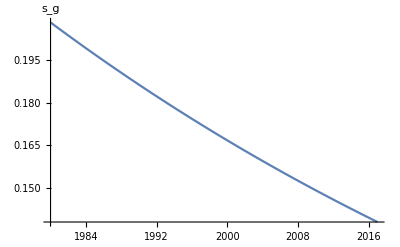

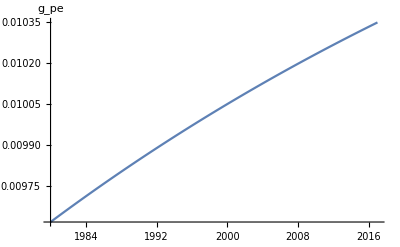

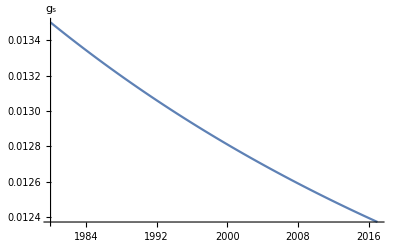

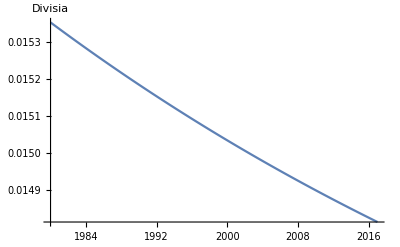

growth rate 1980 = 0.0153516

growth rate 2017 = 0.0148145

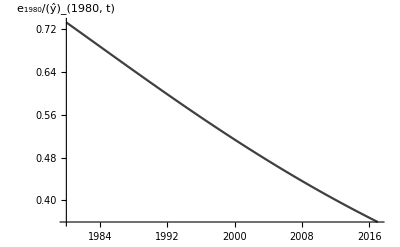

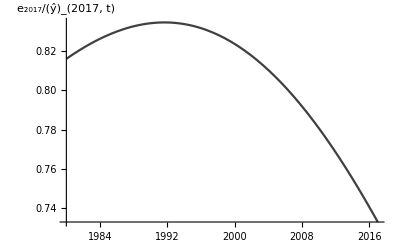

```mathematica
se=e[1980]/y[1980];
Print["consumption share of net income = ",se]

gg=(1-χ)gk+(γ-1)gpg+(χ-γ)gps;
Print["Growth rate Cg = ",gg]

sg[t_]=η(e[t]/Ps[t])^-χ(Pg[t]/Ps[t])^γ;
Plot[sg[t],{t,1980,2017},AxesLabel->{Null,"s_g"}]

gpe[t_]=sg[t] gpg+(1-sg[t]) gps;
Plot[gpe[t],{t,1980,2017},AxesLabel->{Null,"g_pe"}]

Cs[t_]=e[t]/Ps[t](1-sg[t]);
Plot[Cs[t],{t,1980,2017}];
gs[t_]=Simplify[D[Log[Cs[t]],t]];
Plot[gs[t],{t,1980,2017},AxesLabel->{Null,"g_s"}]

Divisia[t_]=Simplify[se(sg[t]gg+(1-sg[t])gs[t])+(1-se)gk];
Plot[Divisia[t],{t,1980,2017},AxesLabel->{Null,"Divisia"}]
Print["growth rate 1980 = ", Divisia[1980]]
Print["growth rate 2017 = ", Divisia[2017]]

Plot[e[1980]/(Mhat[1980,z]+δ k[z]),{z,1980,2017},AxesLabel->{Null,"e_1980/(ŷ)_(1980, t)"},PlotStyle->{GrayLevel[0.25]}]

Plot[e[2017]/(Mhat[2017,z]+δ k[z]),{z,1980,2017},AxesLabel->{Null,"e_2017/(ŷ)_(2017, t)"},PlotStyle->{GrayLevel[0.25]}]
```

```mathematica
FS=Table[{n,NIntegrate[Divisia[t],{t,1980,n}]+nn(n-1980)},{n,1980,2017,0.01}];

Print["bias 1980-base = ",Log[Mhat[1980,z]+δ k[z]]-Log[Mhat[1980,1980]+δ  k[1980]]+nn(z-1980)-FS[[Length[FS],2]]/.z->2017]
Print["bias 2017-base = ",-Log[Mhat[2017,2017]]+Log[Mhat[2017,1980]]+NIntegrate[Divisia[t],{t,1980,2017}]]
```

bias 1980-base = 0.155599

bias 2017-base = 0.564227

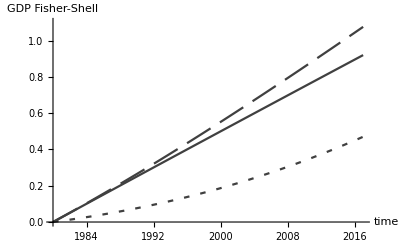

```mathematica
figDivisia=ListPlot[FS,Joined -> True,AxesLabel->{"year","GDP"},PlotRange->{{1980,2017},{0,1.5}},PlotStyle->{GrayLevel[0.25]},PlotRange->{{1980,2017},{0,1}}];
Show[figDivisia,fig2017,fig1980,PlotRange->{{1980,2017},{0,1.1}},AxesLabel->{"time","GDP Fisher-Shell"}]
```

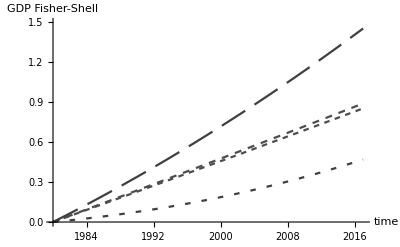

```mathematica
Show[figGDP,fig2017,fig1980,PlotRange->{{1980,2017},{0,1.5}},AxesLabel->{"time","GDP Fisher-Shell"}]
```

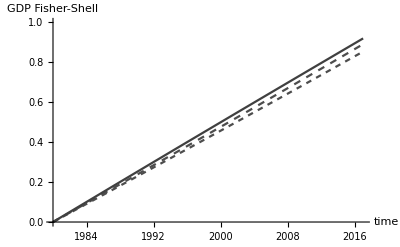

```mathematica
Show[figGDP,figDivisia,PlotRange->{{1980,2017},{0,1}},AxesLabel->{"time","GDP Fisher-Shell"}]
```

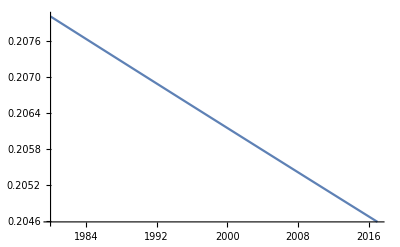

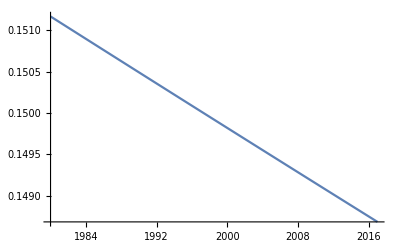

0.208004

0.208004

0.138216

0.148685

```mathematica
Plot[(Pg[1980]cg[t])/(Pg[1980]cg[1980]+Ps[1980]cs[1980]),{t,1980,2017}]
Plot[(Pg[2017]cg[t])/(Pg[2017]cg[1980]+Ps[2017]cs[1980]),{t,1980,2017}]
sg[1980]
(Pg[1980]cg[t])/(Pg[1980]cg[1980]+Ps[1980]cs[1980])/.t->1980
sg[2017]
(Pg[2017]cg[t])/(Pg[2017]cg[1980]+Ps[2017]cs[1980])/.t->2017
```

chained 1980-1990 = 0.250664

chained - Laspeyres_1980 = -0.0139798

chained - Paasche_1990 = 0.0269377

chained - Paasche_2000 = 0.0797856

chained - Paasche_2010 = 0.13729

chained - Paasche_2017 = 0.174622

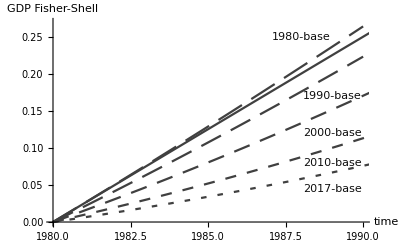

```mathematica
Lapeyres1980[z_]=Log[Mhat[1980,z]+δ k[z]]-Log[Mhat[1980,1980]+δ  k[1980]]+nn(z-1980);
Paasche1990[z_]=Log[Mhat[1990,z]+δ k[z]]-Log[Mhat[1990,1980]+δ  k[1980]]+nn(z-1980);
Paasche2000[z_]=Log[Mhat[2000,z]+δ k[z]]-Log[Mhat[2000,1980]+δ  k[1980]]+nn(z-1980);
Paasche2010[z_]=Log[Mhat[2010,z]+δ k[z]]-Log[Mhat[2010,1980]+δ  k[1980]]+nn(z-1980);
Paasche2017[z_]=Log[Mhat[2017,z]+δ k[z]]-Log[Mhat[2017,1980]+δ  k[1980]]+nn(z-1980);

Print["chained 1980-1990 = ", FS[[1001,2]]]
Print["chained - Laspeyres_1980 = ", FS[[1001,2]]-Lapeyres1980[1990]]
Print["chained - Paasche_1990 = ", FS[[1001,2]]-Paasche1990[1990]]
Print["chained - Paasche_2000 = ", FS[[1001,2]]-Paasche2000[1990]]
Print["chained - Paasche_2010 = ", FS[[1001,2]]-Paasche2010[1990]]
Print["chained - Paasche_2017 = ", FS[[1001,2]]-Paasche2017[1990]]

fig1980=Plot[Lapeyres1980[z],{z,1980,1990},PlotStyle->{Dashing[{0.05,0.02}],GrayLevel[0.25]}];
(*  1980-base *)

fig1990=Plot[Paasche1990[z],{z,1980,1990},PlotStyle->{Dashing[{0.04,0.02}],GrayLevel[0.25]}];
(*  1990-base *)

fig2000=Plot[Paasche2000[z],{z,1980,2000},PlotStyle->{Dashing[{0.03,0.02}],GrayLevel[0.25]}];
(*  2000-base *)

fig2010=Plot[Paasche2010[z],{z,1980,2010},PlotStyle->{Dashing[{0.02,0.02}],GrayLevel[0.25]}];
(*  2010-base *)

Show[figDivisia,fig1980,fig1990,fig2010,fig2000,fig2017,PlotRange->{{1980,1990},{0,.27}},AxesLabel->{"time","GDP Fisher-Shell"},Epilog->{
Text[Style["1980-base",GrayLevel[0.05]],{1988,0.25}],Text[Style["1990-base",GrayLevel[0.05]],{1989,0.17}],Text[Style["2000-base",GrayLevel[0.05]],{1989,0.12}],Text[Style["2010-base",GrayLevel[0.05]],{1989,.08}],Text[Style["2017-base",GrayLevel[0.05]],{1989,.045}]}]
```

Checking Boppart’s Lemma 1

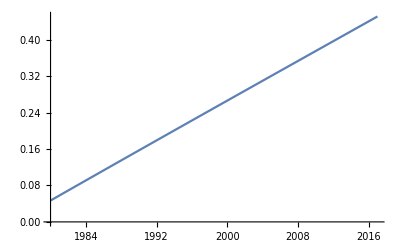

```mathematica
Plot[e[t]^χ-η(1-χ)/(1-γ)Pg[t]^γ Ps[t]^(χ-γ),{t,1980,2017}]
```